Attempt to find likelihood of DM model

Note: input mass of dark matter in GeV since that is what PPPC uses.

PPPC mass of DM range 5 GeV -> 100TeV

#### Make spectral file of model

Define dN/dE for b-bbar that gets the flux of photons given the mass of dark matter (mdm) and ratio x (where x = E/mdm).

```mathematica
Get["/Users/austingottfredson/Indirect-Dark-Matter-Detection/dlNdlxEW.m"];
```

```mathematica
primary="b";
dnde[mdm_,x_,primary_]:=10^(dlNdlxIEW[primary->"γ"][mdm,Log[10,x]])/(Log[10]);
```

Use specfile if you want a spectrum plot for a given mass of DM.

```mathematica
specfile[mdm_]:=With[{i:=10^xp},Table[{i*mdm,dnde[mdm,i,primary]},{xp,-7,0,.2}]];
```

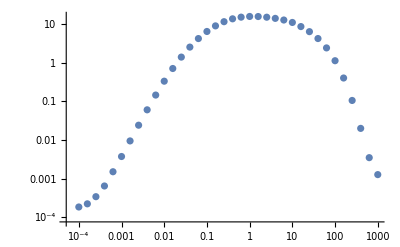

```mathematica
ListLogLogPlot[specfile[1000]]
```

#### Predict normalized energy of model for one energy bin

Import likelihood file and separate the columns

```mathematica
likefile="http://www-glast.stanford.edu/pub_data/1048/like_hercules.txt";
data[likefile_]:=Import[likefile,"Table"];
data2[likefile_]:=Drop[data[likefile],2];
emins[likefile_]:=Flatten[DeleteDuplicates[data2[likefile][[All,1]]]];
emaxs[likefile_]:=Flatten[DeleteDuplicates[data2[likefile][[All,2]]]];
efluxeslikes[likefile_]:=data2[likefile][[All,{1,3,4}]];
loglikes[likefile_]:=Flatten[data2[likefile][[All,4]]];
```

Integrate a generic spectrum, multiplied by E, to get the energy flux. Multiply by 1000 to change from GeV to MeV. The units will just be MeV for an energy bin with a given emin and emax. This is normalized per sing dark matter annihilation.

```mathematica
pred[mdm_,ebin_,primary_,likefile_]:=NIntegrate[dnde[mdm,energy/mdm,primary],{energy,emins[likefile][[ebin]]/1000,emaxs[likefile][[ebin]]/1000}]*1000;
```

#### Eq. 1 from Fermi analysis for one energy bin

Define J factor

```mathematica
jfactor=10^18.1;
```

eflux in MeV/cm^2/s

```mathematica
eflux[sigmav_,mdm_,ebin_,primary_,jfactor_]:=sigmav/(8*Pi*(mdm^2))*pred[mdm,ebin,primary,likefile]*jfactor
```

#### Plot for eflux vs ⟨σv⟩

```mathematica
efluxplot=With[{i:=10^xp},Table[{i,eflux[i,1000,1,primary,jfactor]},{xp,-30,-20,1}]];
```

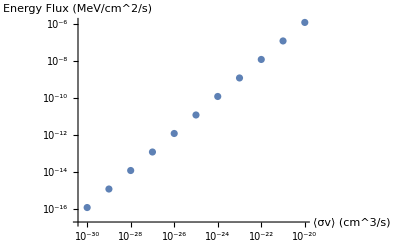

```mathematica
ListLogLogPlot[efluxplot,AxesLabel->{"⟨σv⟩ (cm^3/s)","Energy Flux (MeV/cm^2/s)"}]
```

#### Plot for Log-Likelihood vs mass of DM and sigma*v

Make a loop to separate efluxeslikes into each bin and then train interpolation.
1) separate efluxeslikes into bins
2) train interpolation for each energy bin
3) input eflux into interpolation to get deltaloglike for each energy bin
4) add deltaloglike of each energy bin together
5) Solve for

```mathematica
likebin[bin_,likefile_]:=(Join @@ SequenceCases[efluxeslikes[likefile],{{emins[likefile][[bin]],_,_}}])[[All,{2,3}]]
```

Train interpolation of likelihood file for each bin. The output is the Log-Likelihood.

```mathematica
likeinterp[sigmav_,mdm_,bin_,primary_,likefile_,jfactor_]:=Interpolation[likebin[bin,likefile],eflux[sigmav,mdm,bin,primary,jfactor]];
```

Find the likelihood given eflux found from the eflux function

```mathematica
(*Add together the deltaloglike of each bin given a DM mass and sigmav*)
like[sigmav_,mdm_,primary_,likefile_,jfactor_]:= Sum[likeinterp[sigmav,mdm,bin,primary,likefile,jfactor],{bin,1,24}]
(*Using the sum of each deltaloglike for each bin, find the value of sigmav that gives a (deltaloglike) = (loglike) - (loglikemax) = -2.71/2 *)
(*Return the maximum log like possible*)
loglikemax[mdm_,primary_,likefile_,jfactor_]:=like[10^-30,mdm,primary,likefile,jfactor];sigv[mdm_,primary_,likefile_,jfactor_]:=sv/.FindRoot[like[sv,mdm,primary,likefile,jfactor]-loglikemax[mdm,primary,likefile,jfactor]+2.71/2,{sv,10^-20,10^-30}]
(*Make a table to plot sigmav vs DM mass*)
sigmavplot[primary_,likefile_,jfactor_]:= With[{i:=10^xp},Table[{i, sigv[i,primary,likefile,jfactor]}, {xp, 2.6, 5, 4/20}]];
```

```mathematica
likeplot[mdm_,primary_,likefile_,jfactor_]:=With[{sigv:=10^xp},Table[{sigv,like[sigv,mdm,primary,likefile,jfactor]-loglikemax[mdm,primary,likefile,jfactor]},{xp,-26,-20,.25}]]
```

```mathematica
(*Try plotting log-likelihood vs sigmav for a certain DM mass*)
(*likebbbar=likeplot[1000,primary,likefile,jfactor];*)
```

```mathematica
(*loglikelihood = ListLogLinearPlot[likebbbar,AxesLabel->{"⟨σv⟩ (cm^3/s)","Log-Likelihood"},FrameTicksStyle->Automatic];
c=LogLinearPlot[-2.71/2,{x,10^-26.5,10^-20},PlotPoints->40];
Show[loglikelihood,c,AxesLabel->{"⟨σv⟩ (cm^3/s)","Log-Likelihood"},FrameTicksStyle->Automatic,PlotRange->{-5,0}]*)
```

```mathematica
bbbarplot=sigmavplot[primary,likefile,jfactor];
(*taoplot=sigmavplot["τ",likefile,jfactor];*)
```

InterpolatingFunction::dmval: Input value {-5.09483×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.89473×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.95787×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

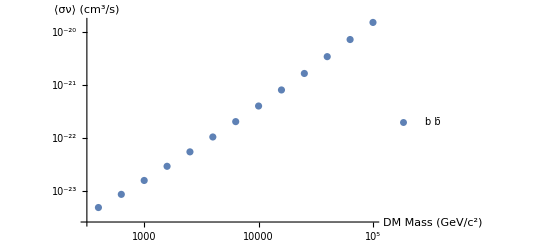

```mathematica
ListLogLogPlot[bbbarplot,AxesLabel->{"DM Mass (GeV/c^2)","⟨σν⟩ (cm^3/s)"},PlotLegends->{primary"b̄","τ^+τ^-"}]
```